## Parallel Setup

```mathematica
LaunchKernels[4]
```

```mathematica
$DistributedContexts=None;
```

```mathematica
<<xAct`xTensor`
ParallelNeeds["xAct`xTensor`"]
```

```mathematica
DefManifold[M,4,{α,β,γ,μ,ν,λ,σ,κ,ρ,η,ξ,χ,ω,ζ}];
```

```mathematica
ParallelEvaluate[DefManifold[M,4,{α,β,γ,μ,ν,λ,σ,κ,ρ,η,ξ,χ,ω,ζ}],Kernels[]];
```

```mathematica
DefMetric[-1,g[-α,-β],CD,{";","∇"},PrintAs->"g"];
```

```mathematica
ParallelEvaluate[DefMetric[-1,g[-α,-β],CD,{";","∇"},PrintAs->"g"],Kernels[]];
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
(*DefChart[polar,M,{0,1,2,3},{tp[],r[],θ[],ϕp[]}];*)
```

```mathematica
(*ParallelEvaluate[DefChart[polar,M,{0,1,2,3},{tp[],r[],θ[],ϕp[]}],Kernels[]];*)
```

```mathematica
(*MetricInBasis[g, -polar, {-1,1,r[]^2,r[]^2Sin[θ[]]^2}];*)
```

```mathematica
(*ParallelEvaluate[MetricInBasis[g, -polar, {-1,1,r[]^2,r[]^2Sin[θ[]]^2}],Kernels[]];*)
```

```mathematica
(*MetricInBasis[g, polar, {-1,1,r[]^(-2),r[]^(-2)Sin[θ[]]^(-2)}];*)
```

```mathematica
(*ParallelEvaluate[MetricInBasis[g, polar, {-1,1,r[]^(-2),r[]^(-2)Sin[θ[]]^(-2)}],Kernels[]];*)
```

```mathematica
(*MetricCompute[g,polar,All,CVSimplify->Simplify];*)
```

```mathematica
(*ParallelEvaluate[MetricCompute[g,polar,All,CVSimplify->Simplify],Kernels[]];*)
```

```mathematica
DefTensor[K[-α,-β],M,Symmetric[{-α,-β}]];
```

```mathematica
ParallelEvaluate[DefTensor[K[-α,-β],M,Symmetric[{-α,-β}]],Kernels[]];
```

```mathematica
DefTensor[A[-α],M];
```

```mathematica
ParallelEvaluate[DefTensor[A[-α],M],Kernels[]];
```

```mathematica
DefTensor[AA[],M,PrintAs->"A"];
```

```mathematica
ParallelEvaluate[DefTensor[AA[],M,PrintAs->"A"],Kernels[]];
```

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None];
```

```mathematica
ParallelEvaluate[SetOptions[ToCanonical,UseMetricOnVBundle->None],Kernels[]];
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
$CovDFormat="Prefix";
```

## Large Definitions

```mathematica
boxsub[-μ_,-ν_]:= (* ∇^γ ∇_γ Subscript[K, μν] *)
Module[{α,β,γ,η,κ,λ},
g[α,β]*PD[-β][PD[-α][K[-μ,-ν]]]+g[α,β]*g[γ,η]*PD[-β][K[-ν,-η]]*PD[-γ][g[-μ,-α]]+g[α,β]*g[γ,η]*PD[-β][K[-μ,-η]]*PD[-γ][g[-ν,-α]]+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-β][g[-μ,-γ]]*PD[-η][g[-κ,-λ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-β][g[-ν,-γ]]*PD[-η][g[-κ,-λ]])/4-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-γ][g[-μ,-β]]*PD[-η][g[-κ,-λ]])/4-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-γ][g[-ν,-β]]*PD[-η][g[-κ,-λ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-β][g[-μ,-κ]]*PD[-η][g[-ν,-λ]])/2-g[α,β]*g[γ,η]*PD[-γ][g[-ν,-α]]*PD[-η][K[-μ,-β]]-g[α,β]*g[γ,η]*PD[-β][g[-α,-γ]]*PD[-η][K[-μ,-ν]]+(g[α,β]*g[γ,η]*PD[-γ][g[-α,-β]]*PD[-η][K[-μ,-ν]])/2-g[α,β]*g[γ,η]*PD[-γ][g[-μ,-α]]*PD[-η][K[-ν,-β]]+(g[α,β]*g[γ,η]*K[-ν,-α]*PD[-η][PD[-β][g[-μ,-γ]]])/2+(g[α,β]*g[γ,η]*K[-μ,-α]*PD[-η][PD[-β][g[-ν,-γ]]])/2-(g[α,β]*g[γ,η]*K[-ν,-α]*PD[-η][PD[-γ][g[-μ,-β]]])/2-(g[α,β]*g[γ,η]*K[-μ,-α]*PD[-η][PD[-γ][g[-ν,-β]]])/2-(g[α,β]*g[γ,η]*K[-ν,-α]*PD[-η][PD[-μ][g[-β,-γ]]])/2-(g[α,β]*g[γ,η]*K[-μ,-α]*PD[-η][PD[-ν][g[-β,-γ]]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-η][g[-ν,-λ]]*PD[-κ][g[-μ,-β]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-η][g[-β,-λ]]*PD[-κ][g[-μ,-γ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-η][g[-β,-λ]]*PD[-κ][g[-ν,-γ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-κ][g[-μ,-γ]]*PD[-λ][g[-β,-η]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-κ][g[-ν,-γ]]*PD[-λ][g[-β,-η]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-β][g[-μ,-γ]]*PD[-λ][g[-η,-κ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-β][g[-ν,-γ]]*PD[-λ][g[-η,-κ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-γ][g[-μ,-β]]*PD[-λ][g[-η,-κ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-γ][g[-ν,-β]]*PD[-λ][g[-η,-κ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-β][g[-μ,-κ]]*PD[-λ][g[-ν,-η]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-κ][g[-μ,-β]]*PD[-λ][g[-ν,-η]])/2-g[α,β]*g[γ,η]*PD[-η][K[-ν,-β]]*PD[-μ][g[-α,-γ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-η][g[-κ,-λ]]*PD[-μ][g[-β,-γ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-λ][g[-η,-κ]]*PD[-μ][g[-β,-γ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-β][g[-η,-λ]]*PD[-μ][g[-γ,-κ]])/4+g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PD[-λ][g[-β,-η]]*PD[-μ][g[-γ,-κ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-β][g[-ν,-κ]]*PD[-μ][g[-η,-λ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-κ][g[-ν,-β]]*PD[-μ][g[-η,-λ]])/2-g[α,β]*g[γ,η]*PD[-η][K[-μ,-β]]*PD[-ν][g[-α,-γ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-η][g[-κ,-λ]]*PD[-ν][g[-β,-γ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-λ][g[-η,-κ]]*PD[-ν][g[-β,-γ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-β][g[-η,-λ]]*PD[-ν][g[-γ,-κ]])/4+g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PD[-λ][g[-β,-η]]*PD[-ν][g[-γ,-κ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-β][g[-μ,-κ]]*PD[-ν][g[-η,-λ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-κ][g[-μ,-β]]*PD[-ν][g[-η,-λ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PD[-μ][g[-β,-κ]]*PD[-ν][g[-η,-λ]])/2];
```

```mathematica
boxsub2=
g[σ,ρ]*PDpolar[-ρ][PDpolar[-σ][K[-μ,-ν]]]+g[σ,ρ]*g[ξ,χ]*PDpolar[-ρ][K[-ν,-χ]]*PDpolar[-ξ][g[-μ,-σ]]+g[σ,ρ]*g[ξ,χ]*PDpolar[-ρ][K[-μ,-χ]]*PDpolar[-ξ][g[-ν,-σ]]+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ρ][g[-μ,-ξ]]*PDpolar[-χ][g[-ω,-ζ]])/4+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ρ][g[-ν,-ξ]]*PDpolar[-χ][g[-ω,-ζ]])/4-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ξ][g[-μ,-ρ]]*PDpolar[-χ][g[-ω,-ζ]])/4-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ξ][g[-ν,-ρ]]*PDpolar[-χ][g[-ω,-ζ]])/4+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-ρ][g[-μ,-ω]]*PDpolar[-χ][g[-ν,-ζ]])/2-g[σ,ρ]*g[ξ,χ]*PDpolar[-ξ][g[-ν,-σ]]*PDpolar[-χ][K[-μ,-ρ]]-g[σ,ρ]*g[ξ,χ]*PDpolar[-ρ][g[-σ,-ξ]]*PDpolar[-χ][K[-μ,-ν]]+(g[σ,ρ]*g[ξ,χ]*PDpolar[-ξ][g[-σ,-ρ]]*PDpolar[-χ][K[-μ,-ν]])/2-g[σ,ρ]*g[ξ,χ]*PDpolar[-ξ][g[-μ,-σ]]*PDpolar[-χ][K[-ν,-ρ]]+(g[σ,ρ]*g[ξ,χ]*K[-ν,-σ]*PDpolar[-χ][PDpolar[-ρ][g[-μ,-ξ]]])/2+(g[σ,ρ]*g[ξ,χ]*K[-μ,-σ]*PDpolar[-χ][PDpolar[-ρ][g[-ν,-ξ]]])/2-(g[σ,ρ]*g[ξ,χ]*K[-ν,-σ]*PDpolar[-χ][PDpolar[-ξ][g[-μ,-ρ]]])/2-(g[σ,ρ]*g[ξ,χ]*K[-μ,-σ]*PDpolar[-χ][PDpolar[-ξ][g[-ν,-ρ]]])/2-(g[σ,ρ]*g[ξ,χ]*K[-ν,-σ]*PDpolar[-χ][PDpolar[-μ][g[-ρ,-ξ]]])/2-(g[σ,ρ]*g[ξ,χ]*K[-μ,-σ]*PDpolar[-χ][PDpolar[-ν][g[-ρ,-ξ]]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-χ][g[-ν,-ζ]]*PDpolar[-ω][g[-μ,-ρ]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-χ][g[-ρ,-ζ]]*PDpolar[-ω][g[-μ,-ξ]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-χ][g[-ρ,-ζ]]*PDpolar[-ω][g[-ν,-ξ]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ω][g[-μ,-ξ]]*PDpolar[-ζ][g[-ρ,-χ]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ω][g[-ν,-ξ]]*PDpolar[-ζ][g[-ρ,-χ]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ρ][g[-μ,-ξ]]*PDpolar[-ζ][g[-χ,-ω]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ρ][g[-ν,-ξ]]*PDpolar[-ζ][g[-χ,-ω]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ξ][g[-μ,-ρ]]*PDpolar[-ζ][g[-χ,-ω]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ξ][g[-ν,-ρ]]*PDpolar[-ζ][g[-χ,-ω]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-ρ][g[-μ,-ω]]*PDpolar[-ζ][g[-ν,-χ]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-ω][g[-μ,-ρ]]*PDpolar[-ζ][g[-ν,-χ]])/2-g[σ,ρ]*g[ξ,χ]*PDpolar[-χ][K[-ν,-ρ]]*PDpolar[-μ][g[-σ,-ξ]]-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-χ][g[-ω,-ζ]]*PDpolar[-μ][g[-ρ,-ξ]])/4+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ζ][g[-χ,-ω]]*PDpolar[-μ][g[-ρ,-ξ]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ρ][g[-χ,-ζ]]*PDpolar[-μ][g[-ξ,-ω]])/4+g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-ν,-σ]*PDpolar[-ζ][g[-ρ,-χ]]*PDpolar[-μ][g[-ξ,-ω]]-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-ρ][g[-ν,-ω]]*PDpolar[-μ][g[-χ,-ζ]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-ω][g[-ν,-ρ]]*PDpolar[-μ][g[-χ,-ζ]])/2-g[σ,ρ]*g[ξ,χ]*PDpolar[-χ][K[-μ,-ρ]]*PDpolar[-ν][g[-σ,-ξ]]-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-χ][g[-ω,-ζ]]*PDpolar[-ν][g[-ρ,-ξ]])/4+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ζ][g[-χ,-ω]]*PDpolar[-ν][g[-ρ,-ξ]])/2-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ρ][g[-χ,-ζ]]*PDpolar[-ν][g[-ξ,-ω]])/4+g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-μ,-σ]*PDpolar[-ζ][g[-ρ,-χ]]*PDpolar[-ν][g[-ξ,-ω]]-(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-ρ][g[-μ,-ω]]*PDpolar[-ν][g[-χ,-ζ]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-ω][g[-μ,-ρ]]*PDpolar[-ν][g[-χ,-ζ]])/2+(g[σ,ρ]*g[ξ,χ]*g[ω,ζ]*K[-σ,-ξ]*PDpolar[-μ][g[-ρ,-ω]]*PDpolar[-ν][g[-χ,-ζ]])/2;
```

```mathematica
boxsub1=
g[α,β]*PDpolar[-β][PDpolar[-α][K[-μ,-ν]]]+g[α,β]*g[γ,η]*PDpolar[-β][K[-ν,-η]]*PDpolar[-γ][g[-μ,-α]]+g[α,β]*g[γ,η]*PDpolar[-β][K[-μ,-η]]*PDpolar[-γ][g[-ν,-α]]+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-β][g[-μ,-γ]]*PDpolar[-η][g[-κ,-λ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-β][g[-ν,-γ]]*PDpolar[-η][g[-κ,-λ]])/4-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-γ][g[-μ,-β]]*PDpolar[-η][g[-κ,-λ]])/4-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-γ][g[-ν,-β]]*PDpolar[-η][g[-κ,-λ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-β][g[-μ,-κ]]*PDpolar[-η][g[-ν,-λ]])/2-g[α,β]*g[γ,η]*PDpolar[-γ][g[-ν,-α]]*PDpolar[-η][K[-μ,-β]]-g[α,β]*g[γ,η]*PDpolar[-β][g[-α,-γ]]*PDpolar[-η][K[-μ,-ν]]+(g[α,β]*g[γ,η]*PDpolar[-γ][g[-α,-β]]*PDpolar[-η][K[-μ,-ν]])/2-g[α,β]*g[γ,η]*PDpolar[-γ][g[-μ,-α]]*PDpolar[-η][K[-ν,-β]]+(g[α,β]*g[γ,η]*K[-ν,-α]*PDpolar[-η][PDpolar[-β][g[-μ,-γ]]])/2+(g[α,β]*g[γ,η]*K[-μ,-α]*PDpolar[-η][PDpolar[-β][g[-ν,-γ]]])/2-(g[α,β]*g[γ,η]*K[-ν,-α]*PDpolar[-η][PDpolar[-γ][g[-μ,-β]]])/2-(g[α,β]*g[γ,η]*K[-μ,-α]*PDpolar[-η][PDpolar[-γ][g[-ν,-β]]])/2-(g[α,β]*g[γ,η]*K[-ν,-α]*PDpolar[-η][PDpolar[-μ][g[-β,-γ]]])/2-(g[α,β]*g[γ,η]*K[-μ,-α]*PDpolar[-η][PDpolar[-ν][g[-β,-γ]]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-η][g[-ν,-λ]]*PDpolar[-κ][g[-μ,-β]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-η][g[-β,-λ]]*PDpolar[-κ][g[-μ,-γ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-η][g[-β,-λ]]*PDpolar[-κ][g[-ν,-γ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-κ][g[-μ,-γ]]*PDpolar[-λ][g[-β,-η]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-κ][g[-ν,-γ]]*PDpolar[-λ][g[-β,-η]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-β][g[-μ,-γ]]*PDpolar[-λ][g[-η,-κ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-β][g[-ν,-γ]]*PDpolar[-λ][g[-η,-κ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-γ][g[-μ,-β]]*PDpolar[-λ][g[-η,-κ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-γ][g[-ν,-β]]*PDpolar[-λ][g[-η,-κ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-β][g[-μ,-κ]]*PDpolar[-λ][g[-ν,-η]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-κ][g[-μ,-β]]*PDpolar[-λ][g[-ν,-η]])/2-g[α,β]*g[γ,η]*PDpolar[-η][K[-ν,-β]]*PDpolar[-μ][g[-α,-γ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-η][g[-κ,-λ]]*PDpolar[-μ][g[-β,-γ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-λ][g[-η,-κ]]*PDpolar[-μ][g[-β,-γ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-β][g[-η,-λ]]*PDpolar[-μ][g[-γ,-κ]])/4+g[α,β]*g[γ,η]*g[κ,λ]*K[-ν,-α]*PDpolar[-λ][g[-β,-η]]*PDpolar[-μ][g[-γ,-κ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-β][g[-ν,-κ]]*PDpolar[-μ][g[-η,-λ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-κ][g[-ν,-β]]*PDpolar[-μ][g[-η,-λ]])/2-g[α,β]*g[γ,η]*PDpolar[-η][K[-μ,-β]]*PDpolar[-ν][g[-α,-γ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-η][g[-κ,-λ]]*PDpolar[-ν][g[-β,-γ]])/4+(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-λ][g[-η,-κ]]*PDpolar[-ν][g[-β,-γ]])/2-(g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-β][g[-η,-λ]]*PDpolar[-ν][g[-γ,-κ]])/4+g[α,β]*g[γ,η]*g[κ,λ]*K[-μ,-α]*PDpolar[-λ][g[-β,-η]]*PDpolar[-ν][g[-γ,-κ]]-(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-β][g[-μ,-κ]]*PDpolar[-ν][g[-η,-λ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-κ][g[-μ,-β]]*PDpolar[-ν][g[-η,-λ]])/2+(g[α,β]*g[γ,η]*g[κ,λ]*K[-α,-γ]*PDpolar[-μ][g[-β,-κ]]*PDpolar[-ν][g[-η,-λ]])/2;
```

```mathematica
pdAA[-α_]:=Module[{β,γ,ζ,η,κ,λ,ξ,ρ,μ,ν},(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*PDpolar[-α][K[-λ,-ν]]*PDpolar[-ζ][g[-β,-γ]]*PDpolar[-η][g[-κ,-μ]])/4+g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-κ,-μ]]*PDpolar[-γ][g[-λ,-ξ]]*PDpolar[-η][g[-ν,-ρ]]-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-κ,-μ]]*PDpolar[-γ][g[-λ,-ν]]*PDpolar[-η][g[-ξ,-ρ]])/2-g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-γ][g[-κ,-μ]]*PDpolar[-η][PDpolar[-α][g[-λ,-ν]]]+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-γ][g[-κ,-λ]]*PDpolar[-η][PDpolar[-α][g[-μ,-ν]]])/2+(g[β,γ]*g[ζ,η]*g[κ,λ]*PDpolar[-α][K[-β,-ζ]]*PDpolar[-η][PDpolar[-γ][g[-κ,-λ]]])/2-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-α][g[-κ,-μ]]*PDpolar[-η][PDpolar[-γ][g[-λ,-ν]]])/2+(g[β,γ]*g[ζ,η]*g[κ,λ]*K[-β,-ζ]*PDpolar[-η][PDpolar[-γ][PDpolar[-α][g[-κ,-λ]]]])/2+g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-γ,-κ]]*PDpolar[-η][g[-μ,-ξ]]*PDpolar[-λ][g[-ν,-ρ]]-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-γ,-κ]]*PDpolar[-η][g[-μ,-ν]]*PDpolar[-λ][g[-ξ,-ρ]])/2-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-η][g[-γ,-κ]]*PDpolar[-λ][PDpolar[-α][g[-μ,-ν]]])/2+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-κ][g[-γ,-η]]*PDpolar[-λ][PDpolar[-α][g[-μ,-ν]]])/4-g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-α][g[-γ,-κ]]*PDpolar[-λ][PDpolar[-η][g[-μ,-ν]]]-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*PDpolar[-α][K[-λ,-ν]]*PDpolar[-κ][g[-β,-ζ]]*PDpolar[-μ][g[-γ,-η]])/2-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*PDpolar[-α][K[-λ,-ν]]*PDpolar[-ζ][g[-β,-γ]]*PDpolar[-μ][g[-η,-κ]])/2+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*PDpolar[-α][K[-η,-ν]]*PDpolar[-ζ][g[-β,-γ]]*PDpolar[-μ][g[-κ,-λ]])/4-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-η][PDpolar[-α][g[-γ,-ν]]]*PDpolar[-μ][g[-κ,-λ]])/2+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-κ,-μ]]*PDpolar[-η][g[-γ,-λ]]*PDpolar[-ν][g[-ξ,-ρ]])/2+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-γ,-κ]]*PDpolar[-η][g[-λ,-μ]]*PDpolar[-ν][g[-ξ,-ρ]])/2-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-κ,-μ]]*PDpolar[-λ][g[-γ,-η]]*PDpolar[-ν][g[-ξ,-ρ]])/4+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-γ,-κ]]*PDpolar[-λ][g[-η,-μ]]*PDpolar[-ν][g[-ξ,-ρ]])/2-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-γ,-κ]]*PDpolar[-μ][g[-η,-λ]]*PDpolar[-ν][g[-ξ,-ρ]])/2+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*K[-β,-ζ]*PDpolar[-μ][g[-κ,-λ]]*PDpolar[-ν][PDpolar[-α][g[-γ,-η]]])/4+(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-κ,-μ]]*PDpolar[-η][g[-γ,-ξ]]*PDpolar[-ρ][g[-λ,-ν]])/2-(g[β,γ]*g[ζ,η]*g[κ,λ]*g[μ,ν]*g[ξ,ρ]*K[-β,-ζ]*PDpolar[-α][g[-κ,-μ]]*PDpolar[-ξ][g[-γ,-η]]*PDpolar[-ρ][g[-λ,-ν]])/4];
```

## Evaluation

```mathematica
MyImport[platform_, file_]:= Module[{path, a},If[platform == "Linux", path = "/home/matthew/Dropbox/Vacio/Mannheim/output/", path = "C:/Users/mgp/Dropbox/Vacio/Mannheim/output/"]; ToExpression[Evaluate[Import[StringJoin[path,file]]]]]
```

```mathematica
(*MyImport["Linuxx","new_gauge/test.txt"];*)
```

```mathematica
MyExport[platform_, destination_, expr_]:= Module[{path},If[platform == "Linux", path = "/home/matthew/Dropbox/Vacio/Mannheim/output/", path = "C:/Users/mgp/Dropbox/Vacio/Mannheim/output/"]; 
Export[StringJoin[path,destination],Evaluate[ToString[Evaluate[expr//InputForm]]],"List"]];
```

```mathematica
length[expr_]:= Length[expr/.{List->Plus}];
```

```mathematica
show[expr_,n_]:= Take[List@@expr,n];
```

```mathematica
dwg[-μ_,-ν_]:= Module[{α,β,γ,ζ},(g[α,β]*g[-μ,-ν]*CD[-β][CD[-α][AA[]]])/6-(g[α,β]*CD[-β][CD[-α][CD[-μ][A[-ν]]]])/2-(g[α,β]*CD[-β][CD[-α][CD[-ν][A[-μ]]]])/2+(g[α,β]*g[γ,ζ]*CD[-ζ][CD[-γ][CD[-β][CD[-α][K[-μ,-ν]]]]])/2+CD[-ν][CD[-μ][AA[]]]/3];
```

```mathematica
dwgnobox[-μ_,-ν_]:=Module[{α,β},(g[α,β]*g[-μ,-ν]*CD[-β][CD[-α][AA[]]])/6-(g[α,β]*CD[-β][CD[-α][CD[-μ][A[-ν]]]])/2-(g[α,β]*CD[-β][CD[-α][CD[-ν][A[-μ]]]])/2+CD[-ν][CD[-μ][AA[]]]/3];
```

```mathematica
Asub = {A[μ_]:> Module[{α,ρ,σ,ν}, 1/2g[ν,α]K[-α,μ]g[ρ,σ]PD[-ν][g[-ρ,-σ]]]};
```

```mathematica
AAsub = {AA[]:>Module[{α,β,γ,ζ,η,κ,λ,μ},-g[α,β]*g[γ,ζ]*g[η,κ]*g[λ,μ]*K[-α,-γ]*PD[-β][g[-η,-λ]]*PD[-ζ][g[-κ,-μ]]/2+(g[α,β]*g[γ,ζ]*g[η,κ]*g[λ,μ]*K[-α,-γ]*PD[-β][g[-η,-κ]]*PD[-ζ][g[-λ,-μ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-ζ][PD[-β][g[-η,-κ]]])/2-(g[α,β]*g[γ,ζ]*g[η,κ]*g[λ,μ]*K[-α,-γ]*PD[-ζ][g[-β,-η]]*PD[-κ][g[-λ,-μ]])/2+(g[α,β]*g[γ,ζ]*g[η,κ]*g[λ,μ]*K[-α,-γ]*PD[-η][g[-β,-ζ]]*PD[-κ][g[-λ,-μ]])/4]};
```

```mathematica
ParallelToCanonical[expr_,n_]:=Module[{},ParallelMap[ToCanonical[Plus@@#]&,Partition[Quiet[PadRight[List@@(SameDummies[expr//Expand]),(Quotient[Length[(SameDummies[expr//Expand])],n]+1)*n]],n]]];
```

```mathematica
ToPD[expr_]:= Expand[ChangeCovD[expr,CD,PD]//ChristoffelToMetric];
```

## Old Old

```mathematica
(*ToPolar[expr_]:= ToCanonical[ToValues[TraceBasisDummy[ Evaluate[expr//ToBasis[polar]//ToBasis[polar]]]]];*)
```

```mathematica
(*ToPolarfast[expr_] := Module[{d,f},d=expr/.{Plus->List};f=ToPolar[#]&/@d;f[[0]]=Plus;ToCanonical[f]];*)
```

```mathematica
(*ParallelToPolar[expr_]:= Plus@@(ParallelToCanonical[ToValues[TraceBasisDummy[ Evaluate[expr//ToBasis[polar]//ToBasis[polar]]]]//Expand,Length[Kernels[]]]);*)
```

```mathematica
(*ParallelToPolarfast[expr_] := Module[{d,f},d=expr/.{Plus->List};f=ParallelToPolar[#]&/@d;f[[0]]=Plus;f];*)
```

```mathematica
term1a = 1/6 {{g, {{α, β}, {, }}}} {{g, {{, }, {μ, ν}}}} ∇_β ∇_α A;
```

```mathematica
term2a =-1/2 {{g, {{α, β}, {, }}}} ∇_β ∇_α ∇_μ {{A, {{}, {ν}}}};
```

```mathematica
term3a = -1/2 {{g, {{α, β}, {, }}}} ∇_β ∇_α ∇_ν {{A, {{}, {μ}}}};
```

```mathematica
term4a = 1/2 {{g, {{α, β}, {, }}}} {{g, {{γ, η}, {, }}}} ∇_η ∇_γ ∇_β ∇_α {{K, {{, }, {μ, ν}}}};
```

```mathematica
term5a = (∇_ν ∇_μ A)/3;
```

```mathematica
term1b = 1/6 g[-μ,-ν]AA[];
```

```mathematica
term2b =-1/2CD[-μ][A[-ν]];
```

```mathematica
term3b = -1/2CD[-ν][A[-μ]];
```

```mathematica
term4b = 1/2 g[α,β]CD[-α]@CD[-β]@K[-μ,-ν];
```

```mathematica
term5b = (∇_ν ∇_μ A)/3;
```

```mathematica
t2b =AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPD[term2a]],Length[Kernels[]]])];
```

```mathematica
t3b = AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPD[term3a]],Length[Kernels[]]])];
```

```mathematica
t23b = AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPD[term4b]],Length[Kernels[]]])];
```

```mathematica
preboxterms =Plus@@ParallelToCanonical[Expand[ToPD[term1b+term2b+term3b+term4b]],Length[Kernels[]]];
```

```mathematica
gpreboxterms =ToCanonical[Plus@@ParallelToCanonical[SameDummies[Expand[preboxterms/.Asub/.AAsub]],Length[Kernels[]]]];
```

```mathematica
t2 = (Plus@@ParallelToCanonical[Expand[ToPD[term4b]],Length[Kernels[]]]);
```

```mathematica
t3 = (Plus@@ParallelToCanonical[Expand[ToPD[t1+t2]],Length[Kernels[]]]);
```

```mathematica
t1
```

```mathematica
AbsoluteTiming[Plus@@ParallelToCanonical[Expand[Expand[ToPolarPD[t1+t2]]],Length[Kernels[]]])
```

```mathematica
t5 = AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[PDpolar[-β][pdAA[-α]]],Length[Kernels[]]])];
```

```mathematica
t5
```

```mathematica
length[boxsub[-μ,-ν]]
```

```mathematica
length[t5[[2]]]
```

```mathematica
t4[[1]]
```

```mathematica
AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[Expand[ToPolarPD[term5a]]],Length[Kernels[]]])]
```

```mathematica
(Plus@@ParallelToCanonical[Expand[Expand[ToPolarPD[term2a+term3a]]],Length[Kernels[]]])
```

```mathematica
term1 =AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPolarPD[term1a]/.AAsub],Length[Kernels[]]])];
```

```mathematica
Speak["Calculation Complete Calculation Complete"];
```

```mathematica
term1[[1]]
```

```mathematica
MyExport["Linuxx","new_gauge/term1",Evaluate[ScreenDollarIndices[term1[[2]]]]]
```

```mathematica
term2 =AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPolarPD[term2a]/.Asub],Length[Kernels[]]])];
```

```mathematica
term3 = term2[[2]]/.{μ->a,ν->b}/.{a->ν,b->μ};
```

```mathematica
term5 =AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPolarPD[term5a]/.AAsub],Length[Kernels[]]])];
```

```mathematica
ReplaceDummies[{α,β,γ,μ,ν,λ,σ,κ,ρ,η,ξ,χ,ω,ζ}]
```

```mathematica
g[α,β]*PDpolar[-β][PDpolar[-α][K[-μ,-ν]]]
```

```mathematica
boxterm1a =Plus@@ParallelToCanonical[PDpolar[-β][Expand[PDpolar[-α][K[-μ,-ν]]]]/.{K[-μ,-ν]:>boxsub2},Length[Kernels[]]];
boxterm1 = AbsoluteTiming[Plus@@ParallelToCanonical[Expand[g[α,β]boxterm1a],Length[Kernels[]]]];
```

```mathematica
Do[
boxtermi = Plus@@ParallelToCanonical[Expand[((List@@boxsub1)[[i]])/.boxsub2],Length[Kernels[]]];
MyExport["Linuxx",StringJoin["new_gauge/box/term",ToString[i],".txt"],boxtermi],{i,2,length[boxsub1]}]
```

## Old Run

```mathematica
polarpdAA =AbsoluteTiming[Plus@@ParallelToCanonical[Expand[ToValues[ParallelToPolarfast[pdAA[-μ]]]/.{μ->0}],Length[Kernels[]]]];
```

```mathematica
ToPolar[expr]
```

```mathematica
Clear[polarpdAA]
```

```mathematica
polarpdAA[[1]]
```

```mathematica
MyExport["Linuxx","new_gauge/polarpdAA0.txt",Evaluate[ScreenDollarIndices[polarpdAA[[2]]]]];
```

```mathematica
Speak["Calculation 1 Complete Calculation 1 Complete"];
```

```mathematica
Clear[polarpdAA];
```

```mathematica
pdpdAA = AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[PDpolar[-β][pdAA[-α]]],Length[Kernels[]]])];
```

```mathematica
pdpdAA[[1]]
```

```mathematica
MyExport["Linuxx","new_gauge/pdpdAA.txt",Evaluate[ScreenDollarIndices[pdpdAA[[2]]]]];
```

```mathematica
Speak["Calculation 2 Complete Calculation 2 Complete"];
```

```mathematica
Clear[pdpdAA];
```

```mathematica
boxterm1a =Plus@@ParallelToCanonical[PDpolar[-β][Expand[PDpolar[-α][K[-μ,-ν]]]]/.{K[-μ,-ν]:>boxsub2},Length[Kernels[]]];
boxterm1 = AbsoluteTiming[Plus@@ParallelToCanonical[Expand[g[α,β]boxterm1a],Length[Kernels[]]]];
```

```mathematica
boxterm1[[1]]
```

```mathematica
MyExport["Linuxx","new_gauge/box/term1.txt",Evaluate[ScreenDollarIndices[boxterm1[[2]]]]]
```

```mathematica
Speak["Calculation 3 Complete Calculation 3 Complete"];
```

```mathematica
Clear[boxterm1];
```

```mathematica
Do[
boxtermi = Plus@@ParallelToCanonical[Expand[((List@@boxsub1)[[i]])/.boxsub2],Length[Kernels[]]];
MyExport["Linuxx",StringJoin["new_gauge/box/term",ToString[i],".txt"],boxtermi],{i,2,length[boxsub1]}]
```

```mathematica
Speak["Calculation 4 Complete Calculation 4 Complete"];
```

```mathematica
gpdpdAA = MyImport["Linuxx","new_gauge/pdpdAA.txt"];
```

```mathematica
gpdpdAA = AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[g[α,β]gpdpdAA],Length[Kernels[]]])];
```

```mathematica
gpdpdAA[[1]]
```

```mathematica
MyExport["Linuxx","new_gauge/gpdpdAA.txt",Evaluate[ScreenDollarIndices[gpdpdAA[[2]]]]];
```

```mathematica
Speak["Calculation All Complete Calculation All Complete"];
```

## Benchmarking

```mathematica
term5b = (∇_ν ∇_μ A)/3;
```

```mathematica
term5c=List@@ScreenDollarIndices[SameDummies[Expand[ToPD[term5b]/.AAsub]]];
```

```mathematica
term5test[i_,n_]:=  (* make i>1 *)AbsoluteTiming[Plus@@ParallelToCanonical[SameDummies[Expand[(Plus@@term5c[[1;;i]])/.AAsub]],n]];
```

```mathematica
benchdata[i_,n_]:=Table[{ii,term5test[ii,nn][[1]],nn},{nn,1,n},{ii,2,i}];
```

```mathematica
benchplotdata[i_,n_]:= Module[{benchdata0},benchdata0=benchdata[i,n];Table[Transpose[{benchdata0[[nn,All]][[All,1]],benchdata0[[nn,All]][[All,2]]}],{nn,1,n}]];
```

```mathematica
(*benchplotrun = AbsoluteTiming[benchplotdata[3,2]];*)
```

```mathematica
(*ListPlot[benchplotrun[[2]],PlotLegends->Table[StringJoin["n=",ToString[n]],{n,1,8}],Joined->True,AxesLabel->{"Number of Terms","Time (s)"},PlotMarkers->Automatic]*)
```

```mathematica
(*Export["C:/Users/mgp/Dropbox/Vacio/Mannheim/hpc/bench.pdf",%]*)
```

```mathematica
mybenchplot[i_,n_]:= {i,term5test[i,n][[1]]};
```

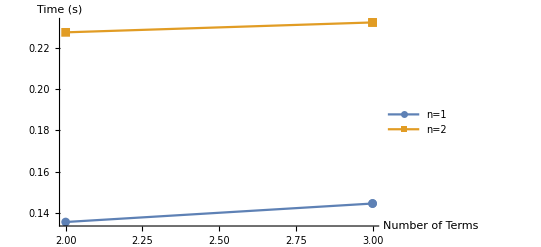

```mathematica
plot =ListPlot[{{mybenchplot[2,1],mybenchplot[3,1]},{mybenchplot[2,2],mybenchplot[3,2]}},PlotLegends->(StringJoin["n=",ToString[#]]&/@{1,2}),Joined->True,AxesLabel->{"Number of Terms","Time (s)"},PlotMarkers->Automatic]
```

```mathematica
Export["/Users/Christy/Dropbox/Vacio/Mannheim/hpc/bench2.eps",%];
```

/Users/Christy/Dropbox/Vacio/Mannheim/hpc/bench2.eps

## New Run

```mathematica
term1a = 1/6 {{g, {{α, β}, {, }}}} {{g, {{, }, {μ, ν}}}} ∇_β ∇_α A;
```

```mathematica
term2a =-1/2 {{g, {{α, β}, {, }}}} ∇_β ∇_α ∇_μ {{A, {{}, {ν}}}};
```

```mathematica
term3a = -1/2 {{g, {{α, β}, {, }}}} ∇_β ∇_α ∇_ν {{A, {{}, {μ}}}};
```

```mathematica
term4a = 1/2 {{g, {{α, β}, {, }}}} {{g, {{γ, η}, {, }}}} ∇_η ∇_γ ∇_β ∇_α {{K, {{, }, {μ, ν}}}};
```

```mathematica
term5a = (∇_ν ∇_μ A)/3;
```

```mathematica
term1b = 1/6 g[-μ,-ν]AA[];
```

```mathematica
term2b =-1/2CD[-μ][A[-ν]];
```

```mathematica
term3b = -1/2CD[-ν][A[-μ]];
```

```mathematica
term4b = 1/2 g[α,β]CD[-α]@CD[-β]@K[-μ,-ν];
```

```mathematica
term5b = (∇_ν ∇_μ A)/3;
```

```mathematica
t2b =AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPD[term2a]],Length[Kernels[]]])];
```

```mathematica
t3b = AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPD[term3a]],Length[Kernels[]]])];
```

```mathematica
t23b = AbsoluteTiming[(Plus@@ParallelToCanonical[Expand[ToPD[term4b]],Length[Kernels[]]])];
```

```mathematica
preboxterms =Plus@@ParallelToCanonical[Expand[ToPD[term1b+term2b+term3b+term4b]],Length[Kernels[]]];
```

```mathematica
gpreboxterms =ToCanonical[Plus@@ParallelToCanonical[SameDummies[Expand[preboxterms/.Asub/.AAsub]],Length[Kernels[]]]];
```

```mathematica
gfpreboxterms[-μ_,-ν_]:= Module[{α,β,γ,ζ,κ,λ,η},(g[α,β]*PD[-β][PD[-α][K[-μ,-ν]]])/2-(g[α,β]*g[γ,ζ]*K[-ν,-α]*PD[-β][PD[-μ][g[-γ,-ζ]]])/4-(g[α,β]*g[γ,ζ]*K[-μ,-α]*PD[-β][PD[-ν][g[-γ,-ζ]]])/4+(g[α,β]*g[γ,ζ]*PD[-β][K[-ν,-ζ]]*PD[-γ][g[-μ,-α]])/2+(g[α,β]*g[γ,ζ]*PD[-β][K[-μ,-ζ]]*PD[-γ][g[-ν,-α]])/2+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-β][g[-μ,-γ]]*PD[-ζ][g[-η,-κ]])/8-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-β][g[-μ,-ν]]*PD[-ζ][g[-η,-κ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-β][g[-ν,-γ]]*PD[-ζ][g[-η,-κ]])/8-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-γ][g[-μ,-β]]*PD[-ζ][g[-η,-κ]])/8-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-γ][g[-ν,-β]]*PD[-ζ][g[-η,-κ]])/8+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-β][g[-μ,-η]]*PD[-ζ][g[-ν,-κ]])/4-(g[α,β]*g[γ,ζ]*PD[-γ][g[-ν,-α]]*PD[-ζ][K[-μ,-β]])/2-(g[α,β]*g[γ,ζ]*PD[-β][g[-α,-γ]]*PD[-ζ][K[-μ,-ν]])/2+(g[α,β]*g[γ,ζ]*PD[-γ][g[-α,-β]]*PD[-ζ][K[-μ,-ν]])/4-(g[α,β]*g[γ,ζ]*PD[-γ][g[-μ,-α]]*PD[-ζ][K[-ν,-β]])/2+(g[α,β]*g[γ,ζ]*g[η,κ]*g[-μ,-ν]*K[-α,-γ]*PD[-ζ][PD[-β][g[-η,-κ]]])/12+(g[α,β]*g[γ,ζ]*K[-ν,-α]*PD[-ζ][PD[-β][g[-μ,-γ]]])/4+(g[α,β]*g[γ,ζ]*K[-μ,-α]*PD[-ζ][PD[-β][g[-ν,-γ]]])/4-(g[α,β]*g[γ,ζ]*K[-ν,-α]*PD[-ζ][PD[-γ][g[-μ,-β]]])/4-(g[α,β]*g[γ,ζ]*K[-μ,-α]*PD[-ζ][PD[-γ][g[-ν,-β]]])/4-(g[α,β]*g[γ,ζ]*K[-ν,-α]*PD[-ζ][PD[-μ][g[-β,-γ]]])/4-(g[α,β]*g[γ,ζ]*K[-μ,-α]*PD[-ζ][PD[-ν][g[-β,-γ]]])/4-(g[α,γ]*g[ζ,η]*g[κ,λ]*g[-μ,-ν]*g[ξ,β]*K[-α,-ζ]*PD[-γ][g[-κ,-ξ]]*PD[-η][g[-λ,-β]])/12-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-ζ][g[-ν,-κ]]*PD[-η][g[-μ,-β]])/4-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-ζ][g[-β,-κ]]*PD[-η][g[-μ,-γ]])/4-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-ζ][g[-β,-κ]]*PD[-η][g[-ν,-γ]])/4+(g[α,γ]*g[ζ,η]*g[κ,λ]*g[-μ,-ν]*g[ξ,β]*K[-α,-ζ]*PD[-γ][g[-κ,-λ]]*PD[-η][g[-ξ,-β]])/24+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-η][g[-μ,-γ]]*PD[-κ][g[-β,-ζ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-η][g[-ν,-γ]]*PD[-κ][g[-β,-ζ]])/4-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-β][g[-μ,-γ]]*PD[-κ][g[-ζ,-η]])/4-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-β][g[-ν,-γ]]*PD[-κ][g[-ζ,-η]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-γ][g[-μ,-β]]*PD[-κ][g[-ζ,-η]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-γ][g[-ν,-β]]*PD[-κ][g[-ζ,-η]])/4-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-β][g[-μ,-η]]*PD[-κ][g[-ν,-ζ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-η][g[-μ,-β]]*PD[-κ][g[-ν,-ζ]])/4-(g[α,γ]*g[ζ,η]*g[κ,λ]*g[-μ,-ν]*g[ξ,β]*K[-α,-ζ]*PD[-η][g[-γ,-κ]]*PD[-λ][g[-ξ,-β]])/12+(g[α,γ]*g[ζ,η]*g[κ,λ]*g[-μ,-ν]*g[ξ,β]*K[-α,-ζ]*PD[-κ][g[-γ,-η]]*PD[-λ][g[-ξ,-β]])/24-(g[α,β]*g[γ,ζ]*PD[-ζ][K[-ν,-β]]*PD[-μ][g[-α,-γ]])/2+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-ζ][g[-η,-κ]]*PD[-μ][g[-β,-γ]])/8+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-κ][g[-ζ,-η]]*PD[-μ][g[-β,-γ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-β][g[-ζ,-κ]]*PD[-μ][g[-γ,-η]])/8+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-ν,-α]*PD[-κ][g[-β,-ζ]]*PD[-μ][g[-γ,-η]])/2-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-β][g[-ν,-η]]*PD[-μ][g[-ζ,-κ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-η][g[-ν,-β]]*PD[-μ][g[-ζ,-κ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-ζ][g[-η,-κ]]*PD[-μ][g[-ν,-β]])/4-(g[α,β]*g[γ,ζ]*PD[-γ][g[-α,-β]]*PD[-μ][K[-ν,-ζ]])/4-(g[α,β]*g[γ,ζ]*PD[-ζ][K[-μ,-β]]*PD[-ν][g[-α,-γ]])/2+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-ζ][g[-η,-κ]]*PD[-ν][g[-β,-γ]])/8+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-κ][g[-ζ,-η]]*PD[-ν][g[-β,-γ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-β][g[-ζ,-κ]]*PD[-ν][g[-γ,-η]])/8+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-μ,-α]*PD[-κ][g[-β,-ζ]]*PD[-ν][g[-γ,-η]])/2-(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-β][g[-μ,-η]]*PD[-ν][g[-ζ,-κ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-η][g[-μ,-β]]*PD[-ν][g[-ζ,-κ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-μ][g[-β,-η]]*PD[-ν][g[-ζ,-κ]])/4+(g[α,β]*g[γ,ζ]*g[η,κ]*K[-α,-γ]*PD[-ζ][g[-η,-κ]]*PD[-ν][g[-μ,-β]])/4-(g[α,β]*g[γ,ζ]*PD[-γ][g[-α,-β]]*PD[-ν][K[-μ,-ζ]])/4];
```

```mathematica
term5 = AbsoluteTiming[Plus@@ParallelToCanonical[SameDummies[Expand[ToPD[term5a]/.AAsub]],Length[Kernels[]]]];
```

```mathematica
term5[[1]]
```

```mathematica
length[term5[[2]]]
```

```mathematica
MyExport["Linuxx","new_gauge/term5.txt",Evaluate[ScreenDollarIndices[term5[[2]]]]]
```

```mathematica
Speak["Calculation Term 5 Complete Calculation Term 5 Complete"];
```

```mathematica
postbox = AbsoluteTiming[Plus@@ParallelToCanonical[SameDummies[Expand[boxsub[-μ,-ν]/.{K[a_,b_]:> gfpreboxterms[a,b]}]],Length[Kernels[]]]];
```

```mathematica
postbox[[1]]
```

```mathematica
length[postbox[[2]]]
```

```mathematica
MyExport["Linuxx","new_gauge/postbox.txt",Evaluate[ScreenDollarIndices[postbox[[2]]]]]
```

```mathematica
Speak["Calculation Postbox Complete Calculation Postbox Complete"];
```